```mathematica
Clear[η,t,ϕ1,ϕ11,ϕ12,ϕ13,ϕ2,ϕ21,ϕ22,ϕ23, η1, η2, η3]
ϕ1[a_,b_,c_,d_]:=e*ϕ11[a,b,c,d]+e^2*ϕ12[a,b,c,d]+e^3*ϕ13[a,b,c,d];
ϕ2[a_,b_,c_,d_]:=e*ϕ21[a,b,c,d]+e^2*ϕ22[a,b,c,d]+e^3*ϕ23[a,b,c,d];
η[a_,b_,c_]:=e* η1[a,b,c]+e^2* η2[a,b,c]+e^3* η3[a,b,c];
```

```mathematica
nhat={1,-e/r D[η[θ,φ,t],θ],-e/(r*Sin[θ])D[η[θ,φ,t],φ]}/(√(1+(-e/r D[η[θ,φ,t],θ])^2+(e/(r*Sin[θ])D[η[θ,φ,t],φ])^2));
```

```mathematica
kinematicst=η[θ,φ,t]+Grad[ϕ1[r,θ,φ,t],{r,θ,φ},"Spherical"].Grad[η[θ,φ,t],{r,θ,φ},"Spherical"]-D[ϕ1[r,θ,φ,t],r]
```

e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t]+1/r^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) (e ϕ11^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ12^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ13^(0,0,1,0)[r,θ,φ,t])+1/r^2(e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) (e ϕ11^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ12^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ13^(0,1,0,0)[r,θ,φ,t])-e ϕ11^(1,0,0,0)[r,θ,φ,t]-e^2 ϕ12^(1,0,0,0)[r,θ,φ,t]-e^3 ϕ13^(1,0,0,0)[r,θ,φ,t]

```mathematica
nopen=(Grad[ϕ2[r,θ,φ,t],{r,θ,φ},"Spherical"]-Grad[ϕ1[r,θ,φ,t],{r,θ,φ},"Spherical"]).nhat
```

-((e Csc[θ] (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) (-1/r Csc[θ] (e ϕ11^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ12^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ13^(0,0,1,0)[r,θ,φ,t])+1/r Csc[θ] (e ϕ21^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ22^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ23^(0,0,1,0)[r,θ,φ,t])))/(r √(1+(e^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t])^2)/r^2+(e^2 (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^2)/r^2)))-(e (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) (-(e ϕ11^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ12^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ13^(0,1,0,0)[r,θ,φ,t])/r+(e ϕ21^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ22^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ23^(0,1,0,0)[r,θ,φ,t])/r))/(r √(1+(e^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t])^2)/r^2+(e^2 (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^2)/r^2))+(-e ϕ11^(1,0,0,0)[r,θ,φ,t]-e^2 ϕ12^(1,0,0,0)[r,θ,φ,t]-e^3 ϕ13^(1,0,0,0)[r,θ,φ,t]+e ϕ21^(1,0,0,0)[r,θ,φ,t]+e^2 ϕ22^(1,0,0,0)[r,θ,φ,t]+e^3 ϕ23^(1,0,0,0)[r,θ,φ,t])/(√(1+(e^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t])^2)/r^2+(e^2 (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^2)/r^2))

```mathematica
curvature=2/r+(-Csc[θ]^2 Derivative[0,2,0][η][θ,φ,t]-Cot[θ] Derivative[1,0,0][η][θ,φ,t]-Derivative[2,0,0][η][θ,φ,t])/r^2+1/r^4(Csc[θ]^2 Derivative[0,2,0][η][θ,φ,t] (Derivative[1,0,0][η][θ,φ,t])^2+Cot[θ] (Derivative[1,0,0][η][θ,φ,t])^3+2 Csc[θ]^2 Derivative[0,1,0][η][θ,φ,t] Derivative[1,0,0][η][θ,φ,t] Derivative[1,1,0][η][θ,φ,t]+3 (Derivative[1,0,0][η][θ,φ,t])^2 Derivative[2,0,0][η][θ,φ,t]);
```

```mathematica
Clear[ρ1,ρ2,We];
normalst=(ρ1*(D[ϕ1[r,θ,φ,t],t]+1/2((Csc[θ]^2 D[ϕ1[r,θ,φ,t],φ]^2)/r^2+D[ϕ1[r,θ,φ,t],θ]^2/r^2+D[ϕ1[r,θ,φ,t],r]^2))-ρ2*(D[ϕ2[r,θ,φ,t],t]+1/2((Csc[θ]^2 D[ϕ2[r,θ,φ,t],φ]^2)/r^2+D[ϕ2[r,θ,φ,t],θ]^2/r^2+D[ϕ2[r,θ,φ,t],r]^2)))-1/We*(curvature);(*e*(1+η[θ,φ,t])*Cos[θ]*Sin[t]*)
```

```mathematica
kinematicstpertr1=Series[kinematicst/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

e (η1[θ,φ,t]-ϕ11^(1,0,0,0)[1,θ,φ,t])+e^2 (η2[θ,φ,t]+Csc[θ]^2 η1^(0,1,0)[θ,φ,t] ϕ11^(0,0,1,0)[1,θ,φ,t]+η1^(1,0,0)[θ,φ,t] ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ12^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t])+e^3 (η3[θ,φ,t]+(-2 η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η2^(1,0,0)[θ,φ,t]) ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ13^(1,0,0,0)[1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] η1^(0,1,0)[θ,φ,t]+η2^(0,1,0)[θ,φ,t]) ϕ11^(0,0,1,0)[1,θ,φ,t]+η1^(0,1,0)[θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+η1^(1,0,0)[θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t])

```mathematica
nopenstpertr1=Series[nopen/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

e (-ϕ11^(1,0,0,0)[1,θ,φ,t]+ϕ21^(1,0,0,0)[1,θ,φ,t])+e^2 (-ϕ12^(1,0,0,0)[1,θ,φ,t]+ϕ22^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t])+e^3 (Csc[θ] η1^(0,1,0)[θ,φ,t] (Csc[θ] ϕ11^(0,0,1,0)[1,θ,φ,t]-Csc[θ] ϕ21^(0,0,1,0)[1,θ,φ,t])+η1^(1,0,0)[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ21^(0,1,0,0)[1,θ,φ,t])-ϕ13^(1,0,0,0)[1,θ,φ,t]+ϕ23^(1,0,0,0)[1,θ,φ,t]-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]+η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]+1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t])

```mathematica
normalstpertr1=Series[normalst/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

-2/We+e ((2 η1[θ,φ,t]+Csc[θ]^2 η1^(0,2,0)[θ,φ,t]+Cot[θ] η1^(1,0,0)[θ,φ,t]+η1^(2,0,0)[θ,φ,t])/We+ρ1 ϕ11^(0,0,0,1)[1,θ,φ,t]-ρ2 ϕ21^(0,0,0,1)[1,θ,φ,t])+e^2 (1/We(-2 (η1[θ,φ,t]^2-η2[θ,φ,t])+Csc[θ]^2 η2^(0,2,0)[θ,φ,t]+Cot[θ] η2^(1,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])+η2^(2,0,0)[θ,φ,t])+ρ1 (ϕ12^(0,0,0,1)[1,θ,φ,t]+1/2 (Csc[θ]^2 (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+(ϕ11^(0,1,0,0)[1,θ,φ,t])^2+(ϕ11^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t])-1/2 ρ2 (2 ϕ22^(0,0,0,1)[1,θ,φ,t]+Csc[θ]^2 (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+(ϕ21^(0,1,0,0)[1,θ,φ,t])^2+(ϕ21^(1,0,0,0)[1,θ,φ,t])^2+2 η1[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t]))+e^3 (1/We(2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t]+η3[θ,φ,t])+Csc[θ]^2 η3^(0,2,0)[θ,φ,t]-Csc[θ]^2 η1^(0,2,0)[θ,φ,t] (η1^(1,0,0)[θ,φ,t])^2-Cot[θ] (η1^(1,0,0)[θ,φ,t])^3+Cot[θ] η3^(1,0,0)[θ,φ,t]-2 Csc[θ]^2 η1^(0,1,0)[θ,φ,t] η1^(1,0,0)[θ,φ,t] η1^(1,1,0)[θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])-3 (η1^(1,0,0)[θ,φ,t])^2 η1^(2,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η2^(0,2,0)[θ,φ,t]-Cot[θ] η2^(1,0,0)[θ,φ,t]-η2^(2,0,0)[θ,φ,t])+η3^(2,0,0)[θ,φ,t])+ρ1 (ϕ13^(0,0,0,1)[1,θ,φ,t]+η2[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t]+η1[θ,φ,t] ϕ12^(1,0,0,1)[1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ11^(0,0,1,0)[1,θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+2 ϕ11^(0,1,0,0)[1,θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])+2 ϕ11^(1,0,0,0)[1,θ,φ,t] (ϕ12^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 ϕ11^(2,0,0,1)[1,θ,φ,t])+ρ2 (-ϕ23^(0,0,0,1)[1,θ,φ,t]-η2[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t]-η1[θ,φ,t] ϕ22^(1,0,0,1)[1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (ϕ21^(0,1,0,0)[1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ21^(0,0,1,0)[1,θ,φ,t] (ϕ22^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,0,1,0)[1,θ,φ,t]))-2 ϕ21^(0,1,0,0)[1,θ,φ,t] (ϕ22^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,1,0,0)[1,θ,φ,t])-2 ϕ21^(1,0,0,0)[1,θ,φ,t] (ϕ22^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 ϕ21^(2,0,0,1)[1,θ,φ,t]))

```mathematica
realklpt[k_,l_,a_,b_]:=Piecewise[{{(√2)*ComplexExpand[Re[SphericalHarmonicY[k,l,a,b]]]//FullSimplify,l>0},{SphericalHarmonicY[k,0,a,0],l==0}}]
```

```mathematica
yk0[k_]:=SphericalHarmonicY[k,0,θ,0]
```

```mathematica
bkl1fun[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_,α_]:=(Clear[c0,d0,m1k,m2k];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;
qk=Integrate[realklpt[k,l,θ,φ]*Sin[θ],{θ,0,α},{φ,0,2Pi}];(*forcing over half sphere*)
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k);fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
(*m1k=If[Δk==0&&ζk==1,0,(nk (-1+ζk))/(4 Δk^2+(-1+ζk)^2)];*)
m2k=(nk *qk(-1+ζk^2))/(4 Δk^2+(-1+ζk^2)^2);m1k=(-2 Δk*nk*qk)/(4 Δk^2+(-1+ζk^2)^2);(*
m2k=If[Δk==0&&ζk==1,0,(2 Δk*nk)/(4 Δk^2+(-1+ζk)^2)];*)

(*If[k==kr,ζk=1];*)
bkl0amp=If[k==m&&l==n,c21*Cos[t]+d21*Sin[t],m1k*Cos[t]+m2k*Sin[t]])(*leading order amplitude of different modes at the resonance frequency kr*)
```

```mathematica
Clear[ohn,rho1,rho2,mu1,mu2,alpha,etaa1,fi11,fi21,b101,b201,b211,b301]
```

```mathematica
b101[s_]:=bkl1fun[ohn,rho1,rho2,mu1,mu2,1,0,2,1,alpha]/.t->s;
b201[s_]:=bkl1fun[ohn,rho1,rho2,mu1,mu2,2,0,2,1,alpha]/.t->s;
b211[s_]:=c21*Cos[s]+d21*Sin[s]/.t->s;
b301[s_]:=bkl1fun[ohn,rho1,rho2,mu1,mu2,3,0,2,1,alpha]/.t->s;

etaa1[a_,b_,c_]:=b101[c]*realklpt[1,0,a,b]+b201[c]*realklpt[2,0,a,b]+b211[c]*realklpt[2,1,a,b]+b301[c]*realklpt[3,0,a,b]

fi11[rr_,a_,b_,c_]:=D[b101[c],c]/1*rr^1*realklpt[1,0,a,b]+D[b201[c],c]/2*rr^2*realklpt[2,0,a,b]+D[b211[c],c]/2*rr^2*realklpt[2,1,a,b]+D[b301[c],c]/3*rr^3*realklpt[3,0,a,b]

fi21[rr_,a_,b_,c_]:=-D[b101[c],c]/(2 rr^2)*realklpt[1,0,a,b]-D[b201[c],c]/(3 rr^3)*realklpt[2,0,a,b]-D[b211[c],c]/(3 rr^3)*realklpt[2,1,a,b]-D[b301[c],c]/(4 rr^4)*realklpt[3,0,a,b]
```

```mathematica
kkl1fun=Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[0,0,1,0][ϕ11][1,θ,φ,t]+Derivative[1,0,0][η1][θ,φ,t] Derivative[0,1,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]]} //Chop;
```

```mathematica
expr=kkl1fun/.{ohn->0.043,rho1->0.86,rho2->0.14,mu1->0.71,mu2->0.29,alpha->Pi/2};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,1,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
k211ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]}
```

0

```mathematica
lkl1fun=η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]} ;
```

```mathematica
nkl1fun=1/We(-2 (η1[θ,φ,t]^2)+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t]))+rho1 (1/2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ11][1,θ,φ,t])^2)+η1[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t])-1/2 rho2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ21][1,θ,φ,t])^2+2 η1[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]} ;
```

```mathematica
bkl2fun[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_,α_]:=(Clear[f1,f2,f3,f4,f5,Δk,f201,wem,We,expr];

expr=kkl1fun/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2,alpha->α};
(*expr=kkl1fun/.{ohn->0.043,rho1->0.86,rho2->0.14,mu1->0.71,mu2->0.29,alpha->Pi/2};*)
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,1,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
kkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]};

expr=lkl1fun/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2,alpha->α};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
lkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]};

expr=nkl1fun/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2,alpha->α};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
nkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]};
bkl1=bkl1fun[oh,ρ1,ρ2,μ1,μ2,k,l,m,n,α];

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);We=wem;(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k);fk=(k(k+1))/(ρ1(k+1)+ρ2*k);gk=(ρ2*k)/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;hk=2*delta*μ2*(k+2);
(*compute the forcing terms*)

qk=Integrate[realklpt[k,l,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,α},{φ,0,2Pi}];

fkl1=TrigReduce[nk*qk*bkl1*Sin[t]-D[kkl1ff,t]-2*Δk*kkl1ff-fk*nkl1ff-gk*D[lkl1ff,t]-hk*lkl1ff];

f1=Integrate[(1/(2Pi))*fkl1,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*fkl1*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*fkl1*Sin[2t],{t,-Pi,Pi}];

bkl1sol=If[k==1,1/4 ((2 f1 t)/Δk-((f4+f5 Δk) Cos[2 t])/(1+Δk^2)+((-f5+f4 Δk) Sin[2 t])/(1+Δk^2)),f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)]//TrigReduce//Simplify//Chop)
```

```mathematica
Integrate[realklpt[1,0,θ,φ]*realklpt[1,0,θ,φ]*Sin[θ],{θ,0,α},{φ,0,2Pi}]
```

1/2 (1-Cos[α]^3)

```mathematica
Integrate[realklpt[2,0,θ,φ]*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,α},{φ,0,2Pi}]
```

1/128 (64-50 Cos[α]-5 Cos[3 α]-9 Cos[5 α])

```mathematica
Integrate[realklpt[1,0,θ,φ]*realklpt[1,0,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}]
```

1/2

```mathematica
bkl1fun[0.043,0.86,0.14,0.71,0.29,2,1,2,1,Pi/2]
```

c21 Cos[t]+d21 Sin[t]

```mathematica
bkl2fun[0.043,0.86,0.14,0.71,0.29,1,0,2,1,Pi/2]
```

-23.9892 t-0.057493 Cos[2 t]+0.00165366 Cos[t] Sin[t]

```mathematica
bkl2fun[0.043,0.86,0.14,0.71,0.29,2,1,2,1,Pi/2]
```

0.377622 d21+(-0.00337142 c21+0.125784 d21) Cos[2 t]+(-0.125784 c21-0.00337142 d21) Sin[2 t]

```mathematica
fkl1
```

0.377622 d21-0.377622 d21 Cos[2 t]+0.377622 c21 Sin[2 t]

```mathematica
kkl1fn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_,α_]:=
(exprog=Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[0,0,1,0][ϕ11][1,θ,φ,t]+Derivative[1,0,0][η1][θ,φ,t] Derivative[0,1,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]]} //Chop;
expr=exprog/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2,alpha->α};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
kkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]}
)
```

```mathematica
lkl1fn[0.043,0.86,0.14,0.71,0.29,2,1,2,1,Pi/2]
```

0

```mathematica
lkl1fn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_,α_]:=
(exprog=η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]} //Chop;
expr=exprog/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2,alpha->α};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
kkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]}
)
```

```mathematica
nkl1fn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_,α_]:=
(exprog=1/We(-2 (η1[θ,φ,t]^2)+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t]))+rho1 (1/2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ11][1,θ,φ,t])^2)+η1[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t])-1/2 rho2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ21][1,θ,φ,t])^2+2 η1[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]} //Chop;
expr=exprog/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2,alpha->α};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
kkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]}
)
```

```mathematica
lkl1fn[0.043,0.86,0.14,0.71,0.29,2,1,2,1,Pi/2]
```

0

```mathematica
Clear[b102f,b212f,b302f,k211f,k301f,etaa2,fi12,fi22,We]
ohn=0.043;rho2=.14;rho1=0.86;mu1=0.71;mu2=0.29;alpha=Pi/2;
b102f[c_]:=bkl2fun[ohn,rho1,rho2,mu1,mu2,1,0,2,1,alpha]/.t->c;
b202f[c_]:=bkl2fun[ohn,rho1,rho2,mu1,mu2,2,0,2,1,alpha]/.t->c;
b212f[c_]:=bkl2fun[ohn,rho1,rho2,mu1,mu2,2,1,2,1,alpha]/.t->c;
b302f[c_]:=bkl2fun[ohn,rho1,rho2,mu1,mu2,3,0,2,1,alpha]/.t->c;
(*k201f[c_]:=k201ff/.t->c;*)
k101f[c_]:=kkl1fn[ohn,rho1,rho2,mu1,mu2,1,0,2,1,alpha]/.t->c;
k201f[c_]:=kkl1fn[ohn,rho1,rho2,mu1,mu2,2,0,2,1,alpha]/.t->c;
k211f[c_]:=kkl1fn[ohn,rho1,rho2,mu1,mu2,2,1,2,1,alpha]/.t->c;
k301f[c_]:=kkl1fn[ohn,rho1,rho2,mu1,mu2,3,0,2,1,alpha]/.t->c;
(*l201f[c_]:=l201ff/.t->c;*)
l101f[c_]:=lkl1fn[ohn,rho1,rho2,mu1,mu2,1,0,2,1,alpha]/.t->c;
l201f[c_]:=lkl1fn[ohn,rho1,rho2,mu1,mu2,2,0,2,1,alpha]/.t->c;
l211f[c_]:=lkl1fn[ohn,rho1,rho2,mu1,mu2,2,1,2,1,alpha]/.t->c;
l301f[c_]:=lkl1fn[ohn,rho1,rho2,mu1,mu2,3,0,2,1,alpha]/.t->c;

etaa2[a_,b_,c_]:=b102f[c]*realklpt[1,0,a,b]+b202f[c]*realklpt[2,0,a,b]+b212f[c]*realklpt[2,1,a,b]+b302f[c]*realklpt[3,0,a,b];
fi12[rr_,a_,b_,c_]:=(D[b102f[c],c]+k101f[c])/1*rr^1*realklpt[1,0,a,b]+(D[b202f[c],c]+k201f[c])/2*rr^2*realklpt[2,1,a,b]+(D[b212f[c],c]+k211f[c])/2*rr^2*realklpt[2,1,a,b]+(D[b302f[c],c]+k301f[c])/3*rr^3*realklpt[3,0,a,b];
fi22[rr_,a_,b_,c_]:=-(D[b102f[c],c]+k101f[c]+l101f[c])/(2*rr^2)*realklpt[1,0,a,b]-(D[b202f[c],c]+k201f[c]+l201f[c])/(3*rr^3)*realklpt[2,0,a,b]-(D[b212f[c],c]+k211f[c]+l211f[c])/(3*rr^3)*realklpt[2,1,a,b]-(D[b302f[c],c]+k301f[c]+l301f[c])/(4*rr^4)*realklpt[3,0,a,b];
```

```mathematica
0.043,0.86,0.14,0.71,0.29,2,1
```

```mathematica
bkl2fun[0.043,0.86,0.14,0.71,0.29,2,1,2,1,alpha]
```

9.39242 d21 t+(-0.00189702 c21+0.0943675 d21) Cos[2 t]+(-0.0943675 c21-0.00189702 d21) Sin[2 t]

```mathematica
bkl2fun[0.043,0.86,0.14,0.71,0.29,1,0,2,1,alpha]
```

-23.9892 t-0.057493 Cos[2 t]+0.00165366 Cos[t] Sin[t]

```mathematica
fi22[a,b,c,d]
```

-(√(3/π) Cos[b] (-23.9892+0.00165366 Cos[d]^2-0.00165366 Sin[d]^2+0.114986 Sin[2 d]))/(4 a^2)-(√(7/π) (-3 Cos[b]+5 Cos[b]^3) (0.777019 Cos[d]^2-0.777019 Sin[d]^2+1.3551 Sin[2 d]))/(16 a^4)+(√(5/(3 π)) Cos[b] Cos[c] Sin[b] (2 (-0.125784 c21-0.00337142 d21) Cos[2 d]-2 (-0.00337142 c21+0.125784 d21) Sin[2 d]))/(2 a^3)-1/(12 a^3)√(5/π) (-1+3 Cos[b]^2) ((-13807363/553291009+(67504154 c21 d21)/1498229915) Cos[d]^2+(-1317602/329780133+(46267119 c21 d21)/102688172) Cos[d]^2+2 (0.00098172-0.000340019 c21^2-0.0412407 c21 d21+0.000340019 d21^2) Cos[2 d]+(68992723/434146454-(67504154 c21^2)/1498229915+(67504154 d21^2)/1498229915) Cos[d] Sin[d]+(75327596/27175141-(46267119 c21^2)/102688172+(46267119 d21^2)/102688172) Cos[d] Sin[d]+(8679255/301796383-(46267119 c21 d21)/102688172) Sin[d]^2+(-3245114/824578259-(67504154 c21 d21)/1498229915) Sin[d]^2-2 (0.146793-0.0206204 c21^2+0.000680037 c21 d21+0.0206204 d21^2) Sin[2 d])

```mathematica
b102f[c]
```

-23.9892 c-0.057493 Cos[2 c]+0.00165366 Cos[c] Sin[c]

```mathematica
kkl2fun=(-2 η1[θ,φ,t] Derivative[1,0,0][η1][θ,φ,t]+Derivative[1,0,0][η2][θ,φ,t]) Derivative[0,1,0,0][ϕ11][1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] Derivative[0,1,0][η1][θ,φ,t]+Derivative[0,1,0][η2][θ,φ,t]) Derivative[0,0,1,0][ϕ11][1,θ,φ,t]+Derivative[0,1,0][η1][θ,φ,t] (Derivative[0,0,1,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ11][1,θ,φ,t]))+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ11][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ12][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ11][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]};
```

```mathematica
nkl2fun=1/We(2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t])-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t] (Derivative[1,0,0][η1][θ,φ,t])^2-Cot[θ] (Derivative[1,0,0][η1][θ,φ,t])^3-2 Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[1,0,0][η1][θ,φ,t] Derivative[1,1,0][η1][θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t])-3 (Derivative[1,0,0][η1][θ,φ,t])^2 Derivative[2,0,0][η1][θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η2][θ,φ,t]-Cot[θ] Derivative[1,0,0][η2][θ,φ,t]-Derivative[2,0,0][η2][θ,φ,t]))+rho1 (η2[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,0,1][ϕ12][1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ11][1,θ,φ,t] (Derivative[0,0,1,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ11][1,θ,φ,t]))+2 Derivative[0,1,0,0][ϕ11][1,θ,φ,t] (Derivative[0,1,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ11][1,θ,φ,t])+2 Derivative[1,0,0,0][ϕ11][1,θ,φ,t] (Derivative[1,0,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ11][1,θ,φ,t])+rho2 (-η2[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t]-η1[θ,φ,t] Derivative[1,0,0,1][ϕ22][1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ21][1,θ,φ,t] (Derivative[0,0,1,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ21][1,θ,φ,t]))-2 Derivative[0,1,0,0][ϕ21][1,θ,φ,t] (Derivative[0,1,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ21][1,θ,φ,t])-2 Derivative[1,0,0,0][ϕ21][1,θ,φ,t] (Derivative[1,0,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]} ;
```

```mathematica
lkl2fun=Csc[θ] Derivative[0,1,0][η1][θ,φ,t] (Csc[θ] Derivative[0,0,1,0][ϕ11][1,θ,φ,t]-Csc[θ] Derivative[0,0,1,0][ϕ21][1,θ,φ,t])+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t]-Derivative[0,1,0,0][ϕ21][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ12][1,θ,φ,t]+η2[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ22][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ11][1,θ,φ,t]+1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]};
```

```mathematica
fi12[d,a,b,c]
```

1/2 d √(3/π) Cos[a] (-23.9892+0.00165366 Cos[c]^2-0.00165366 Sin[c]^2+0.114986 Sin[2 c])+1/12 d^3 √(7/π) (-3 Cos[a]+5 Cos[a]^3) (-2.96544+0.00161157 Cos[c]^2-0.00161157 Sin[c]^2+0.135504 Sin[2 c])-1/4 d^2 √(15/π) Cos[a] Cos[b] Sin[a] (9.39242 d21+2 (-0.0943675 c21-0.00189702 d21) Cos[2 c]-2 (-0.00189702 c21+0.0943675 d21) Sin[2 c])

```mathematica
bkl3fun[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_,α_]:=(Clear[f1,f2,f3,f4,f5,Δk,wem,We,expr];


expr=kkl2fun/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2,alpha->α};
(*expr=kkl1fun/.{ohn->0.043,rho1->0.86,rho2->0.14,mu1->0.71,mu2->0.29,alpha->Pi/2};*)
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
kkl2ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]};

expr=lkl2fun/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2,alpha->α};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
lkl2ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]};

expr=nkl2fun/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2,alpha->α};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
nkl2ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]};

bkl2=bkl2fun[oh,ρ1,ρ2,μ1,μ2,k,l,m,n,α];

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);We=wem;
delta=oh/wem;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k);fk=(k(k+1))/(ρ1(k+1)+ρ2*k);gk=(ρ2*k)/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;hk=2*delta*μ2*(k+2);
(*compute the forcing terms*)

qk=Integrate[realklpt[k,l,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,α},{φ,0,2Pi}];

fkl2=TrigReduce[nk*qk*bkl2*Sin[t]-D[kkl2ff,t]-2*Δk*kkl2ff-fk*nkl2ff-gk*D[lkl2ff,t]-hk*lkl2ff];

fcos=Integrate[(1/Pi)*fkl2*Cos[t],{t,-Pi,Pi}];
fsin=Integrate[(1/Pi)*fkl2*Sin[t],{t,-Pi,Pi}];
g1=Coefficient[fsin,c21]-Coefficient[fsin,c21*d21^2]*d21^2//FullSimplify//Chop;g2=Coefficient[fsin,d21]-Coefficient[fsin,d21*c21^2]*c21^2//FullSimplify//Chop;g3=Coefficient[fcos,c21]-Coefficient[fcos,c21*d21^2]*d21^2//FullSimplify//Chop;g4=Coefficient[fcos,d21]-Coefficient[fcos,d21*c21^2]*c21^2//FullSimplify//Chop;
α1=Coefficient[fcos,c21^3]//Chop;
β1=Coefficient[fcos,d21^3]//Chop;
(*wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
delta=oh/(√wem);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;*)
zetak=wem/we;
dat={g1,g2,g3,g4,α,β1,Δk,wem})
```

```mathematica
bkl3fun[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_,α_]:=(Clear[f1,f2,f3,f4,f5,Δk,wem,We,expr];
expr=kkl2fun/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2,alpha->α};
(*expr=kkl1fun/.{ohn->0.043,rho1->0.86,rho2->0.14,mu1->0.71,mu2->0.29,alpha->Pi/2};*)
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
kkl2ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]};

expr=lkl2fun/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2,alpha->α};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
lkl2ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]};

expr=nkl2fun/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2,alpha->α};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
nkl2ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]};

bkl2=bkl2fun[oh,ρ1,ρ2,μ1,μ2,k,l,m,n,α];

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);We=wem;
delta=oh/wem;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k);fk=(k(k+1))/(ρ1(k+1)+ρ2*k);gk=(ρ2*k)/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;hk=2*delta*μ2*(k+2);
(*compute the forcing terms*)

qk=Integrate[realklpt[k,l,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,α},{φ,0,2Pi}];

fkl2=TrigReduce[nk*qk*bkl2*Sin[t]-D[kkl2ff,t]-2*Δk*kkl2ff-fk*nkl2ff-gk*D[lkl2ff,t]-hk*lkl2ff];

fcos=Integrate[(1/Pi)*fkl2*Cos[t],{t,-Pi,Pi}];
fsin=Integrate[(1/Pi)*fkl2*Sin[t],{t,-Pi,Pi}];
g1=Coefficient[fsin,c21]-Coefficient[fsin,c21*d21^2]*d21^2//FullSimplify//Chop;g2=Coefficient[fsin,d21]-Coefficient[fsin,d21*c21^2]*c21^2//FullSimplify//Chop;g3=Coefficient[fcos,c21]-Coefficient[fcos,c21*d21^2]*d21^2//FullSimplify//Chop;g4=Coefficient[fcos,d21]-Coefficient[fcos,d21*c21^2]*c21^2//FullSimplify//Chop;
α1=Coefficient[fcos,c21^3]//Chop;
β1=Coefficient[fcos,d21^3]//Chop;
(*wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
delta=oh/(√wem);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;*)
zetak=wem/we;
dat={g1,g2,g3,g4,α,β1,Δk,wem})
```

```mathematica
nk*(b212sol*Sin[t])
```

1.51049 Sin[t] (0.377622 d21+(-0.00337142 c21+0.125784 d21) Cos[2 t]+(-0.125784 c21-0.00337142 d21) Sin[2 t])

```mathematica
nk*qk*bkl2*Sin[t]
```

0.755245 Sin[t] (0.377622 d21+(-0.00337142 c21+0.125784 d21) Cos[2 t]+(-0.125784 c21-0.00337142 d21) Sin[2 t])

```mathematica
bkl3fun[0.043,0.86,0.14,0.71,0.29,2,1,2,1,Pi/2]
```

{0.00715156,0.300646,-0.118225,-0.010622,π/2,-0.00506798,0.0201025,8.39161}

```mathematica
bkl3fun[0.043,0.86,0.14,0.71,0.29,2,1,2,1,Pi/2]
```

{0.0119614,0.415632,0.0123819,-0.00888051,π/2,-0.00503938,0.0201025,8.39161}

```mathematica
nk*(b212sol*Sin[t])-nk*qk*bkl2*Sin[t]//FullSimplify
```

0.755245 Sin[t] (0.377622 d21+(-0.00337142 c21+0.125784 d21) Cos[2 t]+(-0.125784 c21-0.00337142 d21) Sin[2 t])

```mathematica
bkl2
```

0.377622 d21+(-0.00337142 c21+0.125784 d21) Cos[2 t]+(-0.125784 c21-0.00337142 d21) Sin[2 t]

```mathematica
kkl2ff//N
```

(c21 Cos[t]+d21 Sin[t]) (-0.00180471 Cos[t]^2-0.23004 Cos[t] Sin[t]+0.00484198 Sin[t]^2)

```mathematica
lkl2ff
```

-(113027565 c21^3 Cos[t]^2 Sin[t])/66282826+c21^2 d21 Cos[t] ((113027565 Cos[t]^2)/66282826-(113027565 Sin[t]^2)/33141413)+d21 ((3503649 Cos[t]^3)/9093885169+(5144949 Cos[t]^2 Sin[t])/215357498+(140554733/43903172+(113027565 d21^2)/66282826) Cos[t] Sin[t]^2-(16973663 Sin[t]^3)/1807379029)+c21 ((6581881 Cos[t]^3)/2687595979+(82641341/46111618+(113027565 d21^2)/33141413) Cos[t]^2 Sin[t]-(1180315 Cos[t] Sin[t]^2)/38281397+(-212335125/150711617-(113027565 d21^2)/66282826) Sin[t]^3)

```mathematica
(126227803 Cos[t] Sin[t]^2)/4093972066//N
```

0.0308326 Cos[t] Sin[t]^2

```mathematica
(1180315 Cos[t] Sin[t]^2)/38281397//N
```

0.0308326 Cos[t] Sin[t]^2

```mathematica
nkl2ff
```

c21^2 d21 Sin[t] (-(141429254 Cos[t]^2)/127093851+(53249213 Sin[t]^2)/158155726)+c21^3 (-(39652871 Cos[t]^3)/270719279+(53249213 Cos[t] Sin[t]^2)/158155726)+c21 ((7558159/32103005+(53249213 d21^2)/158155726) Cos[t]^3-(4596911 Cos[t]^2 Sin[t])/716389978+(-241867761/694924976-(141429254 d21^2)/127093851) Cos[t] Sin[t]^2+(17157745 Sin[t]^3)/4273920619)+d21 ((2024106 Cos[t]^3)/935685397+(58886990/141045459+(53249213 d21^2)/158155726) Cos[t]^2 Sin[t]-(17925505 Cos[t] Sin[t]^2)/2168042574+(-120778724/727671473-(39652871 d21^2)/270719279) Sin[t]^3)

```mathematica
bkl2
```

9.39242 d21 t+(-0.00189702 c21+0.0943675 d21) Cos[2 t]+(-0.0943675 c21-0.00189702 d21) Sin[2 t]

```mathematica
epwe1[we_]:=Module[{sols},sols=ϵ/. Solve[zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,ϵ];
sols=Map[If[Abs[Im[#]]<10^-6,Re[#],#]&,sols];
sols=Select[sols,Element[#,Reals]&&#>0&];
First@sols]
```

```mathematica
epwe2[we_]:=Module[{sols},sols=ϵ/. Solve[zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,ϵ];
sols=Map[If[Abs[Im[#]]<10^-6,Re[#],#]&,sols];
sols=Select[sols,Element[#,Reals]&&#>0&];
First@sols]
```

```mathematica
rr=Table[{we,epwe2[we]},{we,0.1,30,0.1}];
```

Select::normal: Nonatomic expression expected at position 1 in Select[ϵ,#1∈&&#1>0&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

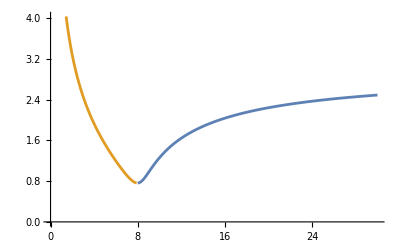

```mathematica
ListLinePlot[{ll,rr}]
```

```mathematica
ll
```

{{0.1,First[{}]},{0.2,First[{}]},{0.3,First[{}]},{0.4,First[{}]},{0.5,First[{}]},{0.6,First[{}]},{0.7,First[{}]},{0.8,First[{}]},{0.9,First[{}]},{1.,First[{}]},{1.1,First[{}]},{1.2,First[{}]},{1.3,First[{}]},{1.4,First[{}]},{1.5,First[{}]},{1.6,First[{}]},{1.7,First[{}]},{1.8,First[{}]},{1.9,First[{}]},{2.,First[{}]},{2.1,First[{}]},{2.2,First[{}]},{2.3,First[{}]},{2.4,First[{}]},{2.5,First[{}]},{2.6,First[{}]},{2.7,First[{}]},{2.8,First[{}]},{2.9,First[{}]},{3.,First[{}]},{3.1,First[{}]},{3.2,First[{}]},{3.3,First[{}]},{3.4,First[{}]},{3.5,First[{}]},{3.6,First[{}]},{3.7,First[{}]},{3.8,First[{}]},{3.9,First[{}]},{4.,First[{}]},{4.1,First[{}]},{4.2,First[{}]},{4.3,First[{}]},{4.4,First[{}]},{4.5,First[{}]},{4.6,First[{}]},{4.7,First[{}]},{4.8,First[{}]},{4.9,First[{}]},{5.,First[{}]},{5.1,First[{}]},{5.2,First[{}]},{5.3,First[{}]},{5.4,First[{}]},{5.5,First[{}]},{5.6,First[{}]},{5.7,First[{}]},{5.8,First[{}]},{5.9,First[{}]},{6.,First[{}]},{6.1,First[{}]},{6.2,First[{}]},{6.3,First[{}]},{6.4,First[{}]},{6.5,First[{}]},{6.6,First[{}]},{6.7,First[{}]},{6.8,First[{}]},{6.9,First[{}]},{7.,First[{}]},{7.1,First[{}]},{7.2,First[{}]},{7.3,First[{}]},{7.4,First[{}]},{7.5,First[{}]},{7.6,First[{}]},{7.7,First[{}]},{7.8,First[{}]},{7.9,First[{}]},{8.,0.76227},{8.1,0.766153},{8.2,0.77498},{8.3,0.788664},{8.4,0.806852},{8.5,0.828959},{8.6,0.854256},{8.7,0.881973},{8.8,0.911374},{8.9,0.941822},{9.,0.972793},{9.1,1.00388},{9.2,1.03478},{9.3,1.06527},{9.4,1.0952},{9.5,1.12447},{9.6,1.15302},{9.7,1.18081},{9.8,1.20783},{9.9,1.23406},{10.,1.25954},{10.1,1.28426},{10.2,1.30824},{10.3,1.33152},{10.4,1.35411},{10.5,1.37604},{10.6,1.39733},{10.7,1.41802},{10.8,1.43811},{10.9,1.45764},{11.,1.47663},{11.1,1.4951},{11.2,1.51308},{11.3,1.53057},{11.4,1.54761},{11.5,1.56421},{11.6,1.58038},{11.7,1.59615},{11.8,1.61153},{11.9,1.62653},{12.,1.64117},{12.1,1.65546},{12.2,1.66942},{12.3,1.68305},{12.4,1.69637},{12.5,1.70939},{12.6,1.72212},{12.7,1.73457},{12.8,1.74676},{12.9,1.75868},{13.,1.77034},{13.1,1.78177},{13.2,1.79295},{13.3,1.80391},{13.4,1.81465},{13.5,1.82517},{13.6,1.83549},{13.7,1.8456},{13.8,1.85552},{13.9,1.86525},{14.,1.8748},{14.1,1.88416},{14.2,1.89336},{14.3,1.90238},{14.4,1.91124},{14.5,1.91995},{14.6,1.9285},{14.7,1.9369},{14.8,1.94515},{14.9,1.95326},{15.,1.96123},{15.1,1.96907},{15.2,1.97677},{15.3,1.98435},{15.4,1.9918},{15.5,1.99913},{15.6,2.00635},{15.7,2.01345},{15.8,2.02043},{15.9,2.02731},{16.,2.03407},{16.1,2.04074},{16.2,2.0473},{16.3,2.05376},{16.4,2.06012},{16.5,2.06639},{16.6,2.07257},{16.7,2.07865},{16.8,2.08465},{16.9,2.09056},{17.,2.09638},{17.1,2.10213},{17.2,2.10779},{17.3,2.11337},{17.4,2.11887},{17.5,2.1243},{17.6,2.12965},{17.7,2.13493},{17.8,2.14014},{17.9,2.14527},{18.,2.15034},{18.1,2.15534},{18.2,2.16028},{18.3,2.16515},{18.4,2.16996},{18.5,2.17471},{18.6,2.1794},{18.7,2.18402},{18.8,2.18859},{18.9,2.1931},{19.,2.19756},{19.1,2.20196},{19.2,2.2063},{19.3,2.21059},{19.4,2.21484},{19.5,2.21903},{19.6,2.22316},{19.7,2.22725},{19.8,2.2313},{19.9,2.23529},{20.,2.23924},{20.1,2.24314},{20.2,2.247},{20.3,2.25081},{20.4,2.25458},{20.5,2.25831},{20.6,2.26199},{20.7,2.26563},{20.8,2.26924},{20.9,2.2728},{21.,2.27632},{21.1,2.27981},{21.2,2.28325},{21.3,2.28666},{21.4,2.29004},{21.5,2.29337},{21.6,2.29668},{21.7,2.29994},{21.8,2.30318},{21.9,2.30637},{22.,2.30954},{22.1,2.31267},{22.2,2.31577},{22.3,2.31884},{22.4,2.32188},{22.5,2.32488},{22.6,2.32786},{22.7,2.33081},{22.8,2.33372},{22.9,2.33661},{23.,2.33947},{23.1,2.3423},{23.2,2.34511},{23.3,2.34788},{23.4,2.35063},{23.5,2.35336},{23.6,2.35605},{23.7,2.35873},{23.8,2.36137},{23.9,2.36399},{24.,2.36659},{24.1,2.36916},{24.2,2.37171},{24.3,2.37424},{24.4,2.37674},{24.5,2.37922},{24.6,2.38167},{24.7,2.38411},{24.8,2.38652},{24.9,2.38891},{25.,2.39128},{25.1,2.39363},{25.2,2.39595},{25.3,2.39826},{25.4,2.40054},{25.5,2.40281},{25.6,2.40506},{25.7,2.40728},{25.8,2.40949},{25.9,2.41168},{26.,2.41385},{26.1,2.416},{26.2,2.41813},{26.3,2.42025},{26.4,2.42235},{26.5,2.42443},{26.6,2.42649},{26.7,2.42853},{26.8,2.43056},{26.9,2.43257},{27.,2.43457},{27.1,2.43655},{27.2,2.43851},{27.3,2.44046},{27.4,2.44239},{27.5,2.4443},{27.6,2.4462},{27.7,2.44809},{27.8,2.44996},{27.9,2.45181},{28.,2.45366},{28.1,2.45548},{28.2,2.45729},{28.3,2.45909},{28.4,2.46088},{28.5,2.46265},{28.6,2.4644},{28.7,2.46615},{28.8,2.46788},{28.9,2.46959},{29.,2.4713},{29.1,2.47299},{29.2,2.47467},{29.3,2.47633},{29.4,2.47799},{29.5,2.47963},{29.6,2.48126},{29.7,2.48287},{29.8,2.48448},{29.9,2.48607},{30.,2.48765}}

```mathematica
fkl2
```

-0.106361 c21 Cos[t]+0.0956149 c21^3 Cos[t]-0.0100652 d21 Cos[t]-0.00506798 c21^2 d21 Cos[t]+0.0956149 c21 d21^2 Cos[t]-0.00506798 d21^3 Cos[t]-0.332935 c21 Cos[3 t]+0.378615 c21^3 Cos[3 t]+0.00498815 d21 Cos[3 t]-0.0152039 c21^2 d21 Cos[3 t]-1.13585 c21 d21^2 Cos[3 t]+0.00506798 d21^3 Cos[3 t]+0.00659479 c21 Sin[t]+0.00506798 c21^3 Sin[t]+0.0273122 d21 Sin[t]+0.0956149 c21^2 d21 Sin[t]+0.00506798 c21 d21^2 Sin[t]+0.0956149 d21^3 Sin[t]+7.09358 d21 t Sin[t]-0.00498815 c21 Sin[3 t]+0.00506798 c21^3 Sin[3 t]-0.332935 d21 Sin[3 t]+1.13585 c21^2 d21 Sin[3 t]-0.0152039 c21 d21^2 Sin[3 t]-0.378615 d21^3 Sin[3 t]